n[1+t]==m+(1+b) (1-d) n[t]

{10,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.}

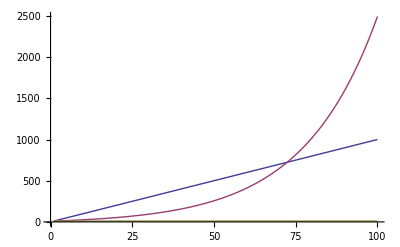

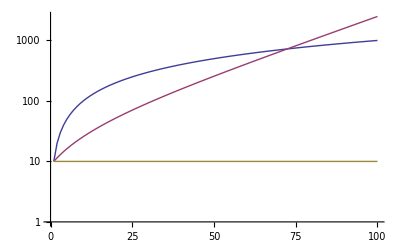

```mathematica
miceEquation=n[t+1]==(1+b) (1-d) n[t]+m
mice=RecurrenceTable[{miceEquation,n[1]==10},n,{t,1,10}];
mice1=mice/.{b->1,d->0.5,m->10};
mice2=mice/.{b->0.1,d->0.05,m->1};
mice3=mice/.{b->1,d->0.5,m->0}
ListPlot[{mice1,mice2,mice3},Joined->True]
ListLogPlot[{mice1,mice2,mice3},Joined->True]
```